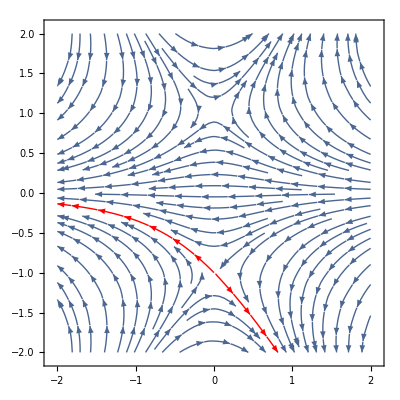

```mathematica
ϕ=Function[p,ω*p-p^3/3];
α=-π;
GraphicsRow[
{ ContourPlot[Re[ϕ[x+ⅈ*y]/.ω->Exp[ⅈ*α]],{x,-2,2},{y,-2,2},Contours->50,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Medium],
StreamPlot[Evaluate[Re[Grad[ϕ[x+ⅈ*y]/.ω->Exp[ⅈ*α],{x,y}]]],{x,-2,2},{y,-2,2},StreamPoints->{{{{-Cos[α/2]+Cos[3α/4]*0.01,Sin[α/2]-Sin[3α/4]*0.01},Red},{{-Cos[α/2]-Cos[3α/4]*0.1,Sin[α/2]+Sin[3α/4]*0.1},Red},Automatic}},ImageSize->Full]}]
```